```mathematica
ClearAll[unblendedCircleSmoothie]

unblendedCircleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[
		{
			fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
			color=Drop[Hue[#]&/@Range[0,1,(1/numCir)],-1],
			circleList,basicCoord,manipulatedCoord,maxRadius,lineList,plotList,styledLines,prePlot
		},
		circleList=Circle[{-maxRadius-5,0},#1]&/@Abs@fourierCoeff;
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}];
		manipulatedCoord=Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}];
		maxRadius=Max[Abs@fourierCoeff];
		lineList=Line[{{-maxRadius-5,0},#1,{0,#1[[2]]}}]&/@manipulatedCoord/.variable->$time;
		styledLines=MapThread[Style,{lineList,color}];
		
		prePlot=MapThread[Times,{fourierCoeff,Cos[(Range[numCir]*(variable+$time))-(Pi/2)]}];
		plotList=Plot[#1,{variable,0,10},PlotStyle->#2]&@@@(Transpose[{prePlot,color}]);
		
		Animate[
			Show[
				Graphics[{Sequence@@#1,Sequence@@#2},Axes->True],
				Plot[#3,{variable,0,10},PlotStyle->#4,PlotRange->All],PlotRange->All
				],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{circleList,styledLines,prePlot,color}]
	
	]
```

```mathematica
ClearAll[circleSmoothie]

circleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierConstant=FourierCosCoefficient[function,variable,0]//ComplexExpand,
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,totalRadius,combinedCir,cirCenter,
		cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,
		lastXCoord,plotCoord
	
	
	},
	
	totalRadius=Total[Abs@fourierCoeff];
	basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*$time]}];
	manipulatedCoord=Join[
		Take[
			Transpose[
			{basicCoord-totalRadius-5,basicCoord/.Cos->Sin}],1],
		Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]];
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius-5,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Echo@Total[MapThread[Times,{fourierCoeff,Cos[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);
	
			
	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,10},PlotRange->Full],PlotRange->All
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord}]
	
	
	]
```

```mathematica
ClearAll[fourierCircleCookBook]
fourierCircleCookBook[function_,variable_Symbol,numCir_Integer]:=
	Row[unblendedCircleSmoothie[function,variable,numCir],
	circleSmoothie[function,variable,numCir]]
```

```mathematica
fourierCircleCookBook[x^2,x,7]
```

-4 Cos[x+$time]+Cos[2 (x+$time)]-4/9 Cos[3 (x+$time)]+1/4 Cos[4 (x+$time)]-4/25 Cos[5 (x+$time)]+1/9 Cos[6 (x+$time)]-4/49 Cos[7 (x+$time)]

Row[,]

```mathematica
circleTest2=Echo@Circle[{-7,0},#1]&/@Abs@Table[FourierCosCoefficient[x^2,x,p],{p,1,5}];
	Animate[
		Show[
			Graphics[{
				(*A list of circles with centers so 
				Circle[center,radius]
				*)
				Circle[{-7,0},4],
				Circle[{-4Cos[t]-7,-4Sin[t]},1],
				Circle[{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},4/9],
				(* One line with a list of coordinates,starting form the center of the first circle going to the edge of the last one. 
					Then the last coordinate is going to be from the edge to the Y-axis
				Line[
				{CenterOfFirstCircle,listOfCoordinates,lastCircleToYAxes}
				]
				lastCircleToYAxes={0,lastYCoord}
				*)
				Line[{
						{-7,0},{-4Cos[t]-7,-4Sin[t]},
						{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},
						{-4Cos[t]+Cos[-2t]-(4/9)Cos[-3t]-7,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]},
						{0,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]}
					}]}
			,Axes->True],
			{
			(*Plot will be the entire function added up,
				Plot[LastXCoord,{variable,0,10}]			
			*)
			Plot[-4Cos[x+t-(Pi/2)]+Cos[-2(x+t)]-(4/9)Cos[-3(x+t)-(Pi/2)],{x,0,10}]
			}
			
	],{t,0,-2Pi},AnimationRunning->False]
	
	(*Making the consecutive list
	Step 1: List of the coordinates will be generated by articifally generaing each one first
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}]
		basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*variable]}]
	
	Step 2: Then generate the list so that only the first coordinate's x-value is subtracted by (maxradius+buffer)	
		manipulatedCoord=Join[Take[Transpose[{basicCoord-maxRadius-5,basicCoord/.Cos->Sin}],1],Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]]
	
	Step 3: Now create a coordinate list where all previous terms are also included within the other values
		Ex: {{-7,0},{-4Cos[t]-7,-4Sin[t]},
			{-4Cos[t]+Cos[-2t]-7,-4Sin[t]+Sin[-2t]},
			{-4Cos[t]+Cos[-2t]-(4/9)Cos[-3t]-7,-4Sin[t]+Sin[-2t]-4/9Sin[-3t]}}
		Method: 
			manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-maxradius-5,0}])
	
	Step 4: For the last coordinate of the list we need to Append (0,lastYValue)
		Take[Take[manipulatedCoord,-1]//Flatten,-1]
	*)
```

Circle[{-7,0},4]

Circle[{-7,0},1]

Circle[{-7,0},4/9]

Circle[{-7,0},1/4]

Circle[{-7,0},4/25]

```mathematica
-4 Cos[x+$time]+Cos[2 (x+$time)]-4/9 Cos[3 (x+$time)]+1/4 Cos[4 (x+$time)]-4/25 Cos[5 (x+$time)]+1/9 Cos[6 (x+$time)]-4/49 Cos[7 (x+$time)]+1/16 Cos[8 (x+$time)]-4/81 Cos[9 (x+$time)]+1/25 Cos[10 (x+$time)]/.Cos[args__]:>Cos[args+Pi/2]
```

4 Sin[x+$time]-Sin[2 (x+$time)]+4/9 Sin[3 (x+$time)]-1/4 Sin[4 (x+$time)]+4/25 Sin[5 (x+$time)]-1/9 Sin[6 (x+$time)]+4/49 Sin[7 (x+$time)]-1/16 Sin[8 (x+$time)]+4/81 Sin[9 (x+$time)]-1/25 Sin[10 (x+$time)]

```mathematica
Animate[Plot[Out[158],{x,0,2Pi}],{$time,0,2Pi}]
```

```mathematica
?Graph
```

```mathematica
circleSmoothie[x^2,x,10]
```

-4 Cos[x+$time]+Cos[2 (x+$time)]-4/9 Cos[3 (x+$time)]+1/4 Cos[4 (x+$time)]-4/25 Cos[5 (x+$time)]+1/9 Cos[6 (x+$time)]-4/49 Cos[7 (x+$time)]+1/16 Cos[8 (x+$time)]-4/81 Cos[9 (x+$time)]+1/25 Cos[10 (x+$time)]

```mathematica
circleSmoothie[x^3,x,10]
```

(24/π-6 π) Cos[x+$time]+3/2 π Cos[2 (x+$time)]+(8/(27 π)-(2 π)/3) Cos[3 (x+$time)]+3/8 π Cos[4 (x+$time)]+(6 (4-25 π^2) Cos[5 (x+$time)])/(625 π)+1/6 π Cos[6 (x+$time)]+(6 (4-49 π^2) Cos[7 (x+$time)])/(2401 π)+3/32 π Cos[8 (x+$time)]+(8/(2187 π)-(2 π)/27) Cos[9 (x+$time)]+3/50 π Cos[10 (x+$time)]

```mathematica
circleSmoothie[x^4,x,10]
```

-8 (-6+π^2) Cos[x+$time]+(-3+2 π^2) Cos[2 (x+$time)]-8/27 (-2+3 π^2) Cos[3 (x+$time)]+1/16 (-3+8 π^2) Cos[4 (x+$time)]-8/625 (-6+25 π^2) Cos[5 (x+$time)]+1/27 (-1+6 π^2) Cos[6 (x+$time)]-(8 (-6+49 π^2) Cos[7 (x+$time)])/2401+(-3/256+π^2/8) Cos[8 (x+$time)]-(8 (-2+27 π^2) Cos[9 (x+$time)])/2187+1/625 (-3+50 π^2) Cos[10 (x+$time)]

```mathematica
FourierCosCoefficient[x^2,x,0]//ComplexExpand
```

(2 π^2)/3

```mathematica
N[(2 π^2)/3]
```

6.57974

```mathematica
FourierSeries[x^2,x,5]//ComplexExpand
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]

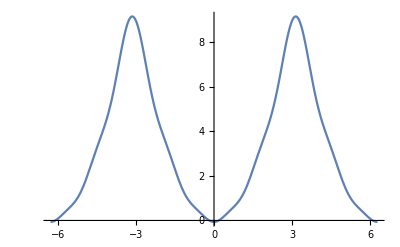

```mathematica
Plot[Out[123],{x,-2Pi,2Pi}]
```

```mathematica
FourierSeries[x^2,x,10]//ComplexExpand
```

π^2/3-4 Cos[x]+Cos[2 x]-4/9 Cos[3 x]+1/4 Cos[4 x]-4/25 Cos[5 x]+1/9 Cos[6 x]-4/49 Cos[7 x]+1/16 Cos[8 x]-4/81 Cos[9 x]+1/25 Cos[10 x]

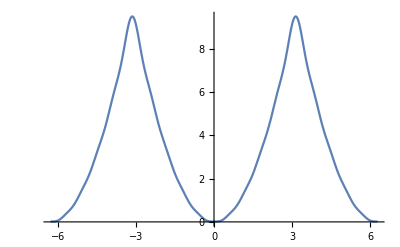

```mathematica
Plot[Out[126],{x,-2Pi,2Pi}]
```

```mathematica
ClearAll[circleSmoothie]

circleSmoothie[function_,variable_Symbol,numCir_Integer]:=
	Block[{
		fourierConstant=FourierCosCoefficient[function,variable,0]//ComplexExpand,
		fourierCoeff=Table[FourierCosCoefficient[function,variable,p],{p,1,numCir}],
		basicCoord,manipulatedCoord,lastYCoord,totalRadius,combinedCir,cirCenter,
		cirArguments,finalPlot,lineSeries,centerOfFirstCir,listOfCoord,lastLinetoYaxis,
		lastXCoord,plotCoord,plotAllign
	
	
	},
	
	totalRadius=Total[Abs@fourierCoeff];
	basicCoord=MapThread[Times,{fourierCoeff,Cos[Range[numCir]*$time]}];
	manipulatedCoord=Join[
		Take[
			Transpose[
			{basicCoord-totalRadius-5,basicCoord/.Cos->Sin}],1],
		Drop[Transpose[{basicCoord,basicCoord/.Cos->Sin}],1]];
	manipulatedCoord=(Plus@@@Table[
								manipulatedCoord[[;;n]],
								{n,1,Length[manipulatedCoord]}]//Prepend[{-totalRadius-5,0}]);
								
	lastYCoord={0,Take[Take[manipulatedCoord,-1]//Flatten,-1]};
	plotCoord=Echo@Total[MapThread[Times,{fourierCoeff,Cos[((Range[numCir])*(variable+$time))]}]];
	cirCenter=Drop[manipulatedCoord,-1];
	cirArguments=Transpose[{cirCenter,Abs@fourierCoeff}];
	
	lastLinetoYaxis=Prepend[Take[Take[manipulatedCoord,-1]//Flatten,-1],0];
	
	combinedCir={Circle[#1,#2]}&@@@(#1&/@cirArguments);
	lineSeries= Line[#1]&@(Append[manipulatedCoord,lastLinetoYaxis]);

	Animate[
			Show[
				Graphics[{Sequence@@#1,#2},Axes->True],
				Plot[#3,{variable,0,10},PlotRange->Full],PlotRange->All
								],
		{$time,0,-2Pi},AnimationRunning->False]&@@Evaluate[{combinedCir,lineSeries,plotCoord}]
	
	
	]
```

```mathematica
circleSmoothie[x^2,x,10]
```

-4 Cos[x+$time]+Cos[2 (x+$time)]-4/9 Cos[3 (x+$time)]+1/4 Cos[4 (x+$time)]-4/25 Cos[5 (x+$time)]+1/9 Cos[6 (x+$time)]-4/49 Cos[7 (x+$time)]+1/16 Cos[8 (x+$time)]-4/81 Cos[9 (x+$time)]+1/25 Cos[10 (x+$time)]

```mathematica
(-4 Cos[x+$time]+Cos[2 (x+$time)]-4/9 Cos[3 (x+$time)]+1/4 Cos[4 (x+$time)]-4/25 Cos[5 (x+$time)]+1/9 Cos[6 (x+$time)]-4/49 Cos[7 (x+$time)]+1/16 Cos[8 (x+$time)]-4/81 Cos[9 (x+$time)]+1/25 Cos[10 (x+$time)])/.(x+$time)->time
```

```mathematica
-4 Cos[time]+Cos[2 time]-4/9 Cos[3 time]+1/4 Cos[4 time]-4/25 Cos[5 time]+1/9 Cos[6 time]-4/49 Cos[7 time]+1/16 Cos[8 time]-4/81 Cos[9 time]+1/25 Cos[10 time]
```

```mathematica
testcir={-4 Cos[time]+Cos[2 time]-4/9 Cos[3 time]+1/4 Cos[4 time]-4/25 Cos[5 time]+1/9 Cos[6 time]-4/49 Cos[7 time]+1/16 Cos[8 time]-4/81 Cos[9 time]+1/25 Cos[10 time]}
```

```mathematica
Animate[Graphics[Circle[#1,1/25],Axes->True],{time,0,-2Pi}]&@Evaluate[{testcir,testcir/.Cos->Sin}]
```

```mathematica
circleSmoothie[SawtoothWave[x],x,5]
```

(2 Cos[x+$time] (-2+Sin[1]+Sin[2]+Sin[3]))/π+(Cos[2 (x+$time)] (Sin[2]+Sin[4]+Sin[6]))/π+(2 Cos[3 (x+$time)] (-2+3 Sin[3]+3 Sin[6]+3 Sin[9]))/(9 π)+(Cos[4 (x+$time)] (Sin[4]+Sin[8]+Sin[12]))/(2 π)+(2 Cos[5 (x+$time)] (-2+5 Sin[5]+5 Sin[10]+5 Sin[15]))/(25 π)

```mathematica
FourierCosSeries[SawtoothWave[x],x,5]//ComplexExpand
```

-3+6/π+π/2-(4 Cos[x])/π-(4 Cos[3 x])/(9 π)-(4 Cos[5 x])/(25 π)+(2 Cos[x] Sin[1])/π+(2 Cos[x] Sin[2])/π+(Cos[2 x] Sin[2])/π+(2 Cos[x] Sin[3])/π+(2 Cos[3 x] Sin[3])/(3 π)+(Cos[2 x] Sin[4])/π+(Cos[4 x] Sin[4])/(2 π)+(2 Cos[5 x] Sin[5])/(5 π)+(Cos[2 x] Sin[6])/π+(2 Cos[3 x] Sin[6])/(3 π)+(Cos[4 x] Sin[8])/(2 π)+(2 Cos[3 x] Sin[9])/(3 π)+(2 Cos[5 x] Sin[10])/(5 π)+(Cos[4 x] Sin[12])/(2 π)+(2 Cos[5 x] Sin[15])/(5 π)

```mathematica
FourierCosCoefficient[SawtoothWave[x],x,5]
```

(2 (-2+5 Sin[5]+5 Sin[10]+5 Sin[15]))/(25 π)

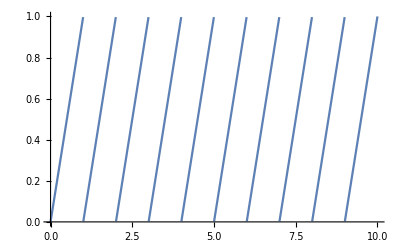

```mathematica
Plot[SawtoothWave[x],{x,0,10}]
```

```mathematica
Animate[Show[Plot[Sin[x+time]+Sin[2(x+time)],{x,0,10},PlotStyle->Red],Plot[Cos[x+time]+Cos[2(x+time)],{x,0,10},PlotStyle->Blue]],{time,0,-2Pi}]
```

```mathematica
Animate[Show[Plot[Sin[x+time],{x,0,10},PlotStyle->Red],Plot[Cos[x+time],{x,0,10},PlotStyle->Blue]],{time,0,-2Pi}]
```

```mathematica
Animate[Show[Plot[Sin[2(x+time)+(Pi/2)],{x,0,10},PlotStyle->Red],Plot[Cos[2(x+time)],{x,0,10},PlotStyle->Blue]],{time,0,-2Pi}]
```